# Scalar scattering with gravity and a cubic/quartic potential

Tree-level p1 + p2 → p3 + p4 scattering of identical real scalars of mass m. The action contains +λ3 phi^3/3! +λ4 phi^4/4! and the canonical massive scalar coupled to gravity. Start in a fresh kernel and evaluate from top to bottom. All momenta p1, p2, p3, p4 denote physical incoming or outgoing momenta as indicated. No loop calculation is performed.

## 1. Load FeynGrav

```mathematica
$LoadAddOns = {"FeynArts"};
<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

Feynman rules for gravity and matter, with FeynCalc notation and FORM support through CalcFormConverter.

The default libraries include cubic and quartic graviton vertices and scalar, Dirac fermion and vector interactions with up to two gravitons. Use the FeynGravImport* commands to load additional libraries.

FeynArts supported models

• Pure general relativity

• Scalar field with a potential minimally coupled to gravity

• Scalar field with a non-minimal kinetic coupling

• Einstein-scalar-Gauss-Bonnet model

The supplied models retain interactions through order κ^2 per vertex. Use matching Model and GenericModel names with FeynCalc-patched FeynArts in a fresh kernel. Models are not initialised automatically.

Evaluate FeynGravCommands[] to list available commands, FeynGravConventions[] to inspect conventions and current settings, and FeynGravHowToCite[] for citation guidance.

## 2. Load the FeynArts model

```mathematica
model = "Single-Scalar-Tensor-Minimal-Coupling";
```

## 3. Generate and display all diagrams

The complete tree has seven diagrams: one quartic scalar contact, scalar exchange in s, t and u, and graviton exchange in s, t and u. The gravitational ghost does not appear in this tree with only external scalars. Higher-valence contacts in the model cannot contribute to a four-external-leg tree.

```mathematica
topologies = CreateTopologies[0, 2 -> 2, Adjacencies -> {3, 4, 5, 6}];
insertions = InsertFields[topologies, {S[1], S[1]} -> {S[1], S[1]}, Model -> model, GenericModel -> model, InsertionLevel -> {Classes}];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/Single-Scalar-Tensor-Minimal-Coupling/Single-Scalar-Tensor-Minimal-Coupling.gen

> $GenericMixing is OFF

generic model {Single-Scalar-Tensor-Minimal-Coupling} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/Single-Scalar-Tensor-Minimal-Coupling/Single-Scalar-Tensor-Minimal-Coupling.mod

> 4 particles (incl. antiparticles) in 3 classes

> $CounterTerms are ON

> 11 vertices

classes model {Single-Scalar-Tensor-Minimal-Coupling} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 2 Classes insertions

> Top. 3: 2 Classes insertions

> Top. 4: 2 Classes insertions

in total: 7 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

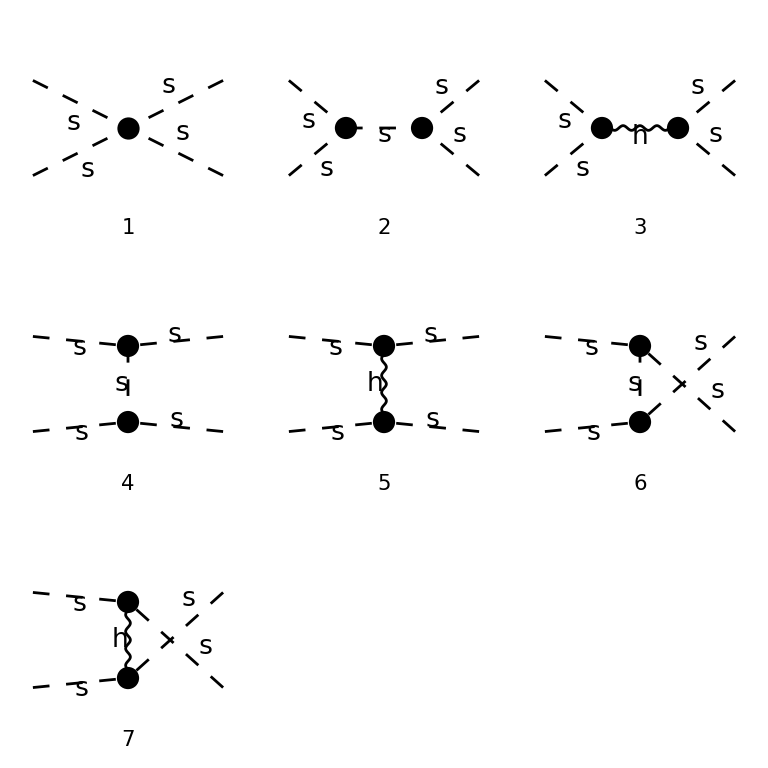

```mathematica
Paint[insertions, ColumnsXRows -> {3, 3},
  Numbering -> Simple,
  SheetHeader -> "Scalar scattering",
  DisplayFunction -> (Print /@ Render[#, ImageSize -> {768, 768}] &)];
```

## 4. Fix the on-shell kinematics

p1 and p2 are incoming; p3 and p4 are outgoing. SetMandelstam receives all momenta incoming, hence the minus signs on p3 and p4. The invariants satisfy s + t + u = 4 m^2. Scalar products are fixed in both four and symbolic D dimensions; the final tree amplitude below is evaluated in four dimensions. These assignments persist in the kernel.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s, t, u, p1, p2, -p3, -p4, m, m, m, m];
```

## 5. Calculate the on-shell amplitude

PreFactor -> 1 retains the Feynman-rule factors of i. The converted diagrams therefore sum to i M. There is no identical-particle phase-space factor in the amplitude. The potential signs are those stated above; the scalar exchanges carry minus λ3^2/(channel - m^2) in M.

```mathematica
ℳ = Collect[Simplify[ExpandScalarProduct[Contract[FeynAmpDenominatorExplicit[FCFAConvert[CreateFeynAmp[insertions, PreFactor -> 1, GaugeRules -> {}, MomentumConservation -> True, Truncated -> True], IncomingMomenta -> {p1, p2}, OutgoingMomenta -> {p3, p4}, LorentzIndexNames -> {μ, ν, ρ, σ, α, β, γ, δ}, ChangeDimension -> 4, Contract -> False, List -> False, Prefactor -> 1] /. {ScalarMass -> m, ScalarLambda3 -> λ3, ScalarLambda4 -> λ4}]]]/I /. D -> 4], {κ^2, λ3^2, λ4}, Factor];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 2 Classes amplitudes

> Top. 3: 2 Classes amplitudes

> Top. 4: 2 Classes amplitudes

in total: 7 Classes amplitudes

```mathematica
mContact = Coefficient[ℳ, λ4] λ4;
mScalar = Coefficient[ℳ, λ3, 2] λ3^2;
mGravity = ℳ ;
```

## 6. Present the amplitude

The amplitude is calculated directly with the on-shell scalar products and s + t + u = 4 m^2. The table separates the calculated result by coupling: the quartic contact, cubic scalar exchange and gravitational exchange. The overall i has been removed, so the displayed result is M. Pole prescriptions are implicit in the original propagators; the rational display is intended away from the poles. No cross section is calculated.

```mathematica
(Grid[{{"Contribution to M", "On-shell expression"}, {"Quartic contact", TraditionalForm[mContact]}, {"Scalar exchange (s, t, u)", TraditionalForm[mScalar]}, {"Graviton exchange (s, t, u)", TraditionalForm[mGravity]}}, Frame -> All, Alignment -> Left])
```

Contribution to M | On-shell expression
Quartic contact | λ4
Scalar exchange (s, t, u) | (λ3^2 (3 m^4-2 m^2 s-2 m^2 t-2 m^2 u+s t+s u+t u))/((m^2-s) (m^2-t) (m^2-u))
Graviton exchange (s, t, u) | λ4-(κ^2 (4 m^4 s t+4 m^4 s u+4 m^4 t u-4 m^2 s^2 t-4 m^2 s^2 u-4 m^2 s t^2-4 m^2 s u^2-4 m^2 t^2 u-4 m^2 t u^2+s^3 t+s^3 u-s^2 t u+s t^3-s t^2 u-s t u^2+s u^3+t^3 u+t u^3))/(8 s t u)+(λ3^2 (3 m^4-2 m^2 s-2 m^2 t-2 m^2 u+s t+s u+t u))/((m^2-s) (m^2-t) (m^2-u))

```mathematica
(ℳ // TraditionalForm)
```

λ4-(κ^2 (4 m^4 s t+4 m^4 s u+4 m^4 t u-4 m^2 s^2 t-4 m^2 s^2 u-4 m^2 s t^2-4 m^2 s u^2-4 m^2 t^2 u-4 m^2 t u^2+s^3 t+s^3 u-s^2 t u+s t^3-s t^2 u-s t u^2+s u^3+t^3 u+t u^3))/(8 s t u)+(λ3^2 (3 m^4-2 m^2 s-2 m^2 t-2 m^2 u+s t+s u+t u))/((m^2-s) (m^2-t) (m^2-u))

### Consistency checks

These checks test the scalar signs, crossing symmetry and decoupling limits. These are tree-level consistency checks, not loop validation.

```mathematica
(kinematicZero[expr_] := Together[expr /. u -> 4 m^2 - s - t] === 0;
checks = {"Quartic sign" -> (mContact === λ4), "Scalar exchanges" -> kinematicZero[mScalar + λ3^2 (1/(s - m^2) + 1/(t - m^2) + 1/(u - m^2))], "s-t crossing" -> kinematicZero[ℳ - (ℳ /. {s -> t, t -> s})], "t-u crossing" -> kinematicZero[ℳ - (ℳ /. {t -> u, u -> t})], "Gravity switched off" -> kinematicZero[(ℳ /. κ -> 0) - mContact - mScalar], "Potential switched off" -> kinematicZero[(ℳ /. {λ3 -> 0, λ4 -> 0}) - mGravity]};
Grid[Prepend[List @@@ checks, {"Check", "Passed"}], Frame -> All, Alignment -> Left])
```

Check | Passed
Quartic sign | True
Scalar exchanges | True
s-t crossing | True
t-u crossing | True
Gravity switched off | True
Potential switched off | False

To change the mass or couplings, replace them in ℳ after completing the calculation. Restart the kernel before switching examples, or call FCClearScalarProducts[] and explicitly reset any other definitions you introduced.